```mathematica
(* plotter requires MaTeX package for LaTeX labels *)
<<MaTeX`
```

### Script for plotting of points classification with single neuron with sigmoid function

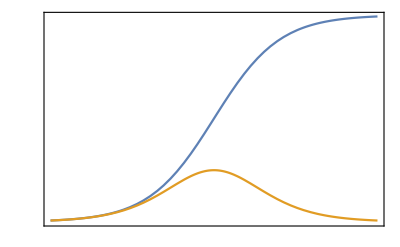

```mathematica
Plot[{1/(1 + Exp[-x]), Exp[-x]/(1 + Exp[-x])^2}, {x, -5, 5},Frame->True, 
PlotLegends->{MaTeX["f(x) = \\dfrac{1}{1 + e^{-x}}", Magnification->1.5], MaTeX["f'(x) = \\dfrac{e^{-x}}{(1 + e^{-x})^2}", Magnification->1.5]},
FrameTicks->{{{#, MaTeX[#, Magnification->1.5]}&/@{0, 0.5, 1}, None}, {{#, MaTeX[#, Magnification->1.5]}&/@{-4,-2, 0, 2, 4}, None}}]
```

### Behaviour of sigmoid function on parameters change

```mathematica
datX = Range[0, 1.0, 0.1];
datY = Range[0, 1.0, 0.1];
(* test dataset, linearly separated points *)
testData = Flatten[Table[{i, j, If[i<j,1,0]},{i, 0, 1,0.1}, {j, 0, 1,0.1}], 1];
```

```mathematica
Manipulate[
Show[
{
Plot3D[{1/(1 + Exp[-(w1 x + w2 y)])}, {x, 0, 1}, {y, 0, 1}, PlotRange->{{0,1}, {0,1}, {-0.1,1}}, 
Mesh->None, ColorFunction->"BlueGreenYellow", 
AxesLabel->{MaTeX["x_1", Magnification->1.5 ],MaTeX["x_2", Magnification->1.5 ], MaTeX["\\text{Class probability}", Magnification->1.5 ]}] ,
ListPointPlot3D[ testData, PlotStyle->Red ]
},

ImageSize->400
], 
{{w1, -7.0043},-10,10, 0.01, Appearance->"Open"}, {{w2, 7.7153},-10,10, 0.01, Appearance->"Open"}
]
```